{-1.77,-0.95,0.,3.04,5.06,5.88}

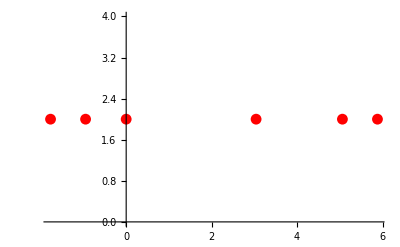

```mathematica
spectrum = {-3.07, -2.25, Mean[{-1.48, -1.12}], Mean[{1.56, 1.92}], 3.76, 4.58};
spectrum = spectrum - spectrum[[3]]
theo = ListPlot[Transpose[{spectrum, Table[2, {i, 1, Length[spectrum]}]}], PlotRange->All, PlotStyle-> {Red}]
```

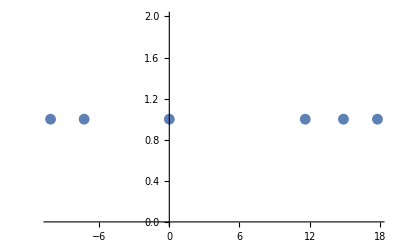

```mathematica
expdata = {-10.155891513286994,-7.280891418325076,0.0,11.623888725596295,14.892032516326106,17.79800673343029};
exp = ListPlot[Transpose[{expdata, Table[1, {i, 1, Length[expdata]}]}], PlotRange->All]
```

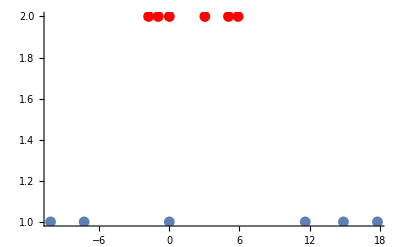

```mathematica
Show[theo, exp, PlotRange-> All]
```